```mathematica
raw=Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/sextupoleResults.json"];
raw= Association[#]&/@raw;
```

```mathematica
groupedData = GroupBy[raw,{#sextName,#bpmName, #magnetConfig, #axis}&];
```

```mathematica
sextNames = raw[[All,"sextName"]]//DeleteDuplicates;
bpmNames=  raw[[All,"bpmName"]]//DeleteDuplicates;
```

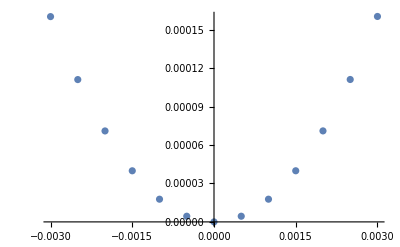

```mathematica
ListPlot[
{#sextOffset,#bpmOffset}&/@groupedData[[10]]
]
```

```mathematica
allImg= Table[
img = GraphicsGrid[
Table[
activeData = {
10^3#sextOffset,
10^3#bpmOffset
}&/@groupedData[{sextName,bpmName,magnetConfig,axis}];

ListPlot[
activeData,
PlotLabel->{sextName,bpmName,magnetConfig,axis},
ImageSize->400,
Frame->True,
FrameLabel->{sextName<>" offset [mm]", bpmName<>" offset [mm]"},
(*PlotStyle->ColorData["Rainbow"][Rescale[Max[Abs[activeData[[All,2]]]],{0,0.5}]]*)
ColorFunctionScaling->False,
ColorFunction->(ColorData["Rainbow"][Rescale[Max[Abs[#2]],{0,0.2}]]&),
Joined->True
],

{sextName,sextNames},
{bpmName,bpmNames}

],
ImageSize->4000
];

Export["~/"<>StringRiffle[{magnetConfig,axis},"_"]<>".png",img];
img,

{magnetConfig,{"BCON","BMAX"}},
{axis,{"x","y"}}
];
```

## Y data with offsets

```mathematica
raw=Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/sextupoleResults_withOffsets.json"];
raw= Association[#]&/@raw;
```

```mathematica
groupedData = GroupBy[raw,{#sextName,#bpmName, #magnetConfig, #axis}&];
```

```mathematica
allImg= Table[
img = GraphicsGrid[
Table[
activeData = {
10^3#sextOffset,
10^3#bpmOffset
}&/@groupedData[{sextName,bpmName,magnetConfig,axis}];

ListPlot[
activeData,
PlotLabel->{sextName,bpmName,magnetConfig,axis},
ImageSize->400,
Frame->True,
FrameLabel->{sextName<>" offset [mm]", bpmName<>" offset [mm]"},
(*PlotStyle->ColorData["Rainbow"][Rescale[Max[Abs[activeData[[All,2]]]],{0,0.5}]]*)
ColorFunctionScaling->False,
ColorFunction->(ColorData["Rainbow"][Rescale[Max[Abs[#2]],{0,0.2}]]&),
Joined->True
],

{sextName,sextNames},
{bpmName,bpmNames}

],
ImageSize->4000
];

Export["~/"<>StringRiffle[{magnetConfig,axis},"_"]<>"_withOffset.png",img];
img,

{magnetConfig,{"BCON","BMAX"}},
{axis,{"y"}}
];
```